1

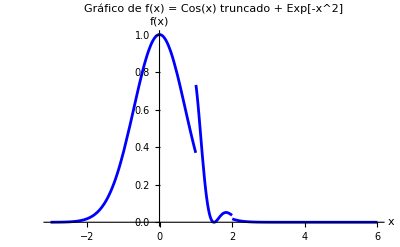

```mathematica
(*Definir la función f[x_] que es coseno truncado y exp(-x^2)*)
f[a_,x_]:=Exp[-x^2]*Piecewise[{{Cos[2*Pi*x/a],a<=x<=2 a}},0]+Exp[-x^2]
(*Graficar la función f[x] para un valor fijo de a*)
a = 1

Plot[f[a ,x],{x,-3,6},PlotRange->All,PlotStyle->Blue,AxesLabel->{"x","f(x)"},PlotLabel->"Gráfico de f(x) = Cos(x) truncado + Exp[-x^2]"]
```

1

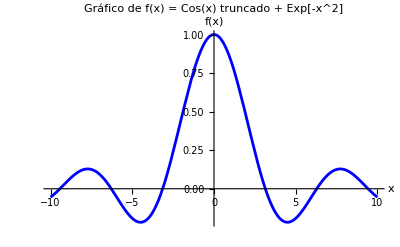

```mathematica
(*Definir la función f[x_] que es coseno truncado y exp(-x^2)*)
f[a_,x_]:=Sinc[a*x]
(*Graficar la función f[x] para un valor fijo de a*)
a = 1

Plot[f[a ,x],{x,-10,10},PlotRange->All,PlotStyle->Blue,AxesLabel->{"x","f(x)"},PlotLabel->"Gráfico de f(x) = Cos(x) truncado + Exp[-x^2]"]
```